```mathematica
(*2nd order*)
Clear[h]
f1=Expand[2*(h/2-x)*(h-x)]/h^2;
f2=(4x*h-4*x^2)/h^2;
f3=(2*x^2-x*h)/h^2;
(*f1=1-x/h;
f2=-4x*(x-h)/h^2;
f3=x/h;*)
f={f1,f2,f3};
Kloc=Table[-Integrate[D[f[[i]],x]*f[[j]],{x,0,h}],{i,1,3},{j,1,3}]
Mloc=Table[Integrate[f[[i]]*f[[j]],{x,0,h}],{i,1,3},{j,1,3}]
```

{{1/2,2/3,-1/6},{-2/3,0,2/3},{1/6,-2/3,-1/2}}

{{(2 h)/15,h/15,-h/30},{h/15,(8 h)/15,h/15},{-h/30,h/15,(2 h)/15}}

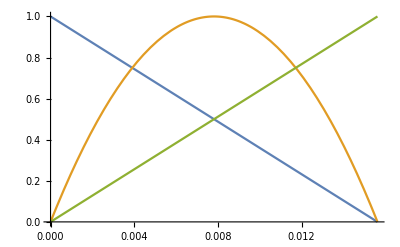

```mathematica
h=1./64;
Plot[f,{x,0,h}]
```

```mathematica
N=64;(*Number of elements*)
T=0.5;(*Final time*)
P=2;(*Order of polynoms on each element*)
τ=1./8*(1/N)^(0.5*(P+1));(*time step*)
h=1/N;(*space step*)
```

```mathematica
Integrate[D[f[[1]],x]*f[[1]],{x,0,h}]
```

-1/2

```mathematica
a=D[f[[1]],x]*f[[1]]
```

((-3 h+4 x) (h^2-3 h x+2 x^2))/h^4

```mathematica
Integrate[f[[1]]*f[[1]],{x,0,h}]
```

-1+1/h+h/3